```mathematica
ClearAll["Global`*"]
```

```mathematica
{Low$40mM,Low$100mM,Middle$100mM, High$40mM, High$100mM} ={{{-5.993759750390016,-0.09636363636363637},{-5.120124804992199,-0.09313131313131318},{-4.439937597503899,-0.0850505050505051},{-3.9719188767550695,-0.05595959595959599},{-3.6099843993759744,-0.028484848484848502},{-3.2979719188767547,-0.0014141414141414232},{-2.9360374414976596,0.003434343434343401},{-2.4243369734789386,0.007474747474747467},{-2.018720748829953,0.010707070707070693}}, {{-5.993759750390016,-0.07292929292929295},{-5.120124804992199,-0.07090909090909092},{-4.433697347893915,-0.06282828282828284},{-4.433697347893915,-0.06282828282828284},{-3.9656786271450852,-0.04262626262626262},{-3.60374414976599,-0.022424242424242458},{-3.29173166926677,-0.006666666666666654},{-2.92355694227769,-0.0022222222222222365},{-2.436817472698907,0.00262626262626643},{-2.018720748829953,0.006666666666666626}}, {{-5.993759750390016,-0.07090909090909092},{-5.276131045241809,-0.07090909090909092},{-4.602184087363494,-0.06808080808080808},{-4.121684867394695,-0.05555555555555558},{-3.7659906396255844,-0.044646464646464656},{-3.44773790951638,-0.00424242424242427},{-3.092043681747269,0.016767676767676765},{-2.455538221528861,0.026868686868686847}}, {{-5.993759750390016,-.9111111111111109*10^(-1)},{-5.993759750390016,-.9111111111111109*10^(-1)},{-5.993759750390016,-.8989898989898992*10^(-1)},{-5.388455538221528,-.8707070707070708*10^(-1)},{-5.213728549141965,-.882828282828283*10^(-1)},{-4.702028081123244,-.850505050505051*10^(-1)},{-4.527301092043681,-.850505050505051*10^(-1)},{-4.234009360374415,-.7616161616161615*10^(-1)},{-4.059282371294851,-.7979797979797981*10^(-1)},{-3.6973478939157562,.6040404040404038*10^(-1)},{-3.510140405616224,.616161616161616*10^(-1)},{-3.2480499219968797,.6121212121212119*10^(-1)},{-3.0608424336973474,.6121212121212119*10^(-1)},{-2.705148205928236,.5919191919191916*10^(-1)},{-2.530421216848673,.5919191919191916*10^(-1)}},  {{-5.993759750390016,-0.07090909090909092},{-5.213728549141965,-0.07212121212121214},{-4.527301092043681,-0.07010101010101011},{-4.527301092043681,-0.07010101010101011},{-4.059282371294851,-0.06808080808080808},{-3.5163806552262087,0.04424242424242422},{-3.0608424336973474,0.04424242424242422},{-2.530421216848673,0.037373737373737365}}};
```

```mathematica
{High$10mM,Middle$10mM,Low$10mM, High$20, Middle$20,Low$20}={{{-5.392970000,-.1010000000`},{-5.213000000,-.9780000000*10^(-1)},{-5.212000000,-.9570000000*10^(-1)},{-4.710860000,-.9550000000*10^(-1)},{-4.531000000,-.9320000000*10^(-1)},{-4.530000000,-.8610000000*10^(-1)},{-4.237920000,-.8350000000*10^(-1)},{-4.058000000,-.8556000000*10^(-1)},{-4.057000000,-.8350000000*10^(-1)},{-3.878110000,-.6800000000*10^(-1)},{-3.698000000,-.7400000000*10^(-1)},{-3.670000000,-.5985000000*10^(-1)},{-3.562880000,.7150000000*10^(-1)},{-3.561000000,-.3980000000*10^(-1)},{-3.510000000,.6750000000*10^(-1)},{-3.475000000,.6336000000*10^(-1)},{-3.346000000,.7605000000*10^(-1)},{-3.198730000,.7750000000*10^(-1)},{-3.174000000,.7940000000*10^(-1)},{-3.064000000,.7800000000*10^(-1)},{-2.697240000,.8060000000*10^(-1)},{-2.558000000,.8230000000*10^(-1)},{-2.525000000,.8160000000*10^(-1)}}, {{-6,-.1029000000`},{-5.283,-.1007000000`},{-5.283,-.1026500000`},{-4.601,-.9370000000*10^(-1)},{-4.601,-.9645000000*10^(-1)},{-4.13,-.8170000000*10^(-1)},{-4.13,-.7180000000*10^(-1)},{-3.913,-.6400000000*10^(-1)},{-3.913,-.5350000000*10^(-1)},{-3.771,-.3710000000*10^(-1)},{-3.771,-.4570000000*10^(-1)},{-3.666,-.3330000000*10^(-1)},{-3.666,-.3140000000*10^(-1)},{-3.583,-.7000000000*10^(-2)},{-3.583,.3650000000*10^(-2)},{-3.515,.7300000000*10^(-2)},{-3.515,.1400000000*10^(-1)},{-3.322,.3390000000*10^(-1)},{-3.322,.3000000000*10^(-1)},{-3.035,.5320000000*10^(-1)},{-3.035,.3880000000*10^(-1)},{-2.58,.5870000000*10^(-1)},{-2.58,.5060000000*10^(-1)},{-2.336,.4850000000*10^(-1)}}, {{-6,-1.118*10^(-1)},{-5.124,-1.0435000000*10^(-1)},{-4.442,-.857000000*10^(-1)},{-3.969,-.44150000000*10^(-1)},{-3.421,-.190000000*10^(-1)},{-2.763,.1400000000*10^(-1)},{-2.368,.1880000000*10^(-1)}}, {{-5.211831629,-.627*10^(-1)},{-4.530177984,-.478*10^(-1)},{-4.290730039,-.41*10^(-2)},{-4.146910470,.1845*10^(-1)},{-3.903089987,.324*10^(-1)},{-3.480172006,.415*10^(-1)},{-2.628932138,.5035*10^(-1)}}, {{-5.392544977,-.584*10^(-1)},{-4.709965389,-.444*10^(-1)},{-4.429457060,-.120*10^(-1)},{-4.133122186,.343*10^(-1)},{-3.838631998,.396*10^(-1)},{-3.747146969,.424*10^(-1)},{-3.607303047,.444*10^(-1)}}, {{-7.00,-.620*10^(-1)},{-5.12,-.560*10^(-1)},{-4.82,-.530*10^(-1)},{-4.52,-.450*10^(-1)},{-4.34,-.390*10^(-1)},{-4.12,-.320*10^(-1)},{-3.92,-.260*10^(-1)},{-3.70,-.160*10^(-1)},{-3.56,-.139*10^(-1)},{-3.37,-.9*10^(-2)},{-3.13,-.6*10^(-2)},{-2.86,-.24*10^(-2)},{-2.4,-.5*10^(-3)}}};
```

```mathematica
(*Единицы длины-нанометры, единицы заряда - электроны*)
P=1; (*Доля заряда липида, участвующая в адсорбции*)
k=1.38*10^(-23); (*Константа больцмана*)
T=293; (*Температура*)
ϵ=80; (*Диэлектрическая проницаемость воды*)
el=1;(*Заряд электрона равен единице*)


z0=0.2; (*Толщина штерновского слоя*)
(*c0=10^-2*0.6;*) (*Концентрация электролита в шт/nm^3 (=10 mM/l)*)
ϕT=0.025; (*kT/e = 25 mV*)
adopc=0.6; (*Площадь на молекулу DOPC*)
acl=1.2; (*Площадь на молекулу кардиолипин*)
Mcl=1494; (*молярка кардиолипина*)
Mdopc=770; (*молярка DOPC*)
(*Связь минимальной толщины полимерного слоя с объёмом одного монолизина, считая, что один монолизин распластывается на половину кардиолиина (аCL = 2*adopc)*)

σ0=-P((2 el θ$e α)/acl)(*Поверхностная плотность заряда кардиолипина c поправкой на адсорбцию ионов на него*);

stot=(1/2) CLip ((adopc (1-α))/Mdopc+(acl α)/Mcl)(*Полная площадь мембраны, нормированная на объём ячейки*);

θ$e= K1(* Sinh[-( Subscript[ϕ, 0] /ϕT)]((2 acl c0 λ)/α); не получаются нужные значения*);

Γ = (1/(2 K4 γ acl stot))(2α K4 stot + K4 γ acl Cc + acl - √((2 K4 α stot-K4 γ acl Cc)^2+2 K4 acl (2 α stot+γ acl)+acl^2));
θ =  (acl (1 + Cc γ K4 )+2α K4 stot θ$lim - acl √((-8 Cc γ K4^2 stot α θ$lim)/acl + (1 + Cc γ K4 + (2α K4 stot  θ$lim)/acl)^2))/(4α K4 stot);
(* σp=el((2α)/(acl G)); пока не нужно *)
(*G=stot (σp/el);*)
(*Доля площади мембраны, покрытой белком*)
σ1=σ0 + el Γ (1 - γ (1 - θ$e));
(* σ2=Min[(σ0-σ1 β K1)/(1-β) ,0];(*K3 - степень сгущения заряженного липида под лизином*) пока не нужно *)
(* 
	α - массовая доля липида,
	acl - площадь на молекулу кардиолипина = 1.2,
	Сc - начальная концентрация мономеров полилизина в растворе,
	γ, G - геометрический параметр, указывающий на долю адсорбированных мономеров лизина,
	K4 - константа связывания ((K+)/(K-)) полимера и мембраны,
	β0, Subscript[θ, lim] - предельная доля полимерного покрытия,
	λ - Дебаевская длина - расстояние,на которое распространяется действие электрического поля отдельного заряда,
	σ1 - Плотность поверхностного заряда мембраны,
	σ0 - плотность поверхностного заряда мембраны в отсутствии полимера,
	σp - плотность заряда, вносимая полимером,
	c0 - концентрация электролита,
	Γ - плотность покрытия мономеров лизина,
	Subscript[θ, e], K1 - Коээфициент, учитывающий адсорбцию катионов на молекулах кардиолипина,
*)
	

ϕ1=2ϕT ArcSinh[σ1/(4c0 el λ)];

 Subscript[ψ, 2] = 2ϕT(θ ArcSinh[α(1/γ-1)/(2λ acl c0)] +(1 - θ) ArcSinh[(-α θ$e)/(2λ acl c0)]);

Homogeneous=ϕ1; 
Inhomogeneous = Subscript[ψ, 2];
```

```mathematica
Subscript[ϕ, 0] = 10^High$10mM[[1,1]];
c0r = 10^-2 * 0.6;
αr = 1;
λr = 3;
Sinh[-( Subscript[ϕ, 0] /ϕT)]((2 acl c0r λr)/αr);
```

```mathematica
F1[Cc_]=Homogeneous;
F[Cc_] =  Inhomogeneous;
```

```mathematica
(* Homogeneous *)
err$Hom$High10mM = Total[(F1[10^High$10mM[[All,1]]]-High$10mM[[All,2]])^2];
su$Hom$High10mM = {λ->3,c0->10^-2*0.6,α -> 1, K1 -> 0.2, γ -> γh, CLip -> CL, K4-> 10^K4$h};
err$Hom$High10mM = err$Hom$High10mM/.su$Hom$High10mM;

err$Hom$Low40mM=Total[(F1[10^Low$40mM[[All,1]]]-Low$40mM[[All,2]])^2];
su$Hom$Low40mM={λ->1.9, c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$l,γ->γl};
err$Hom$Low40mM=err$Hom$Low40mM/.su$Hom$Low40mM;
err$Hom$Low100mM=Total[(F1[10^Low$100mM[[All,1]]]-Low$100mM[[All,2]])^2];
su$Hom$Low100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$l,  γ->γl};
err$Hom$Low100mM=err$Hom$Low100mM/.su$Hom$Low100mM;
err$Hom$Middle100mM=Total[(F1[10^Middle$100mM[[All,1]]]-Middle$100mM[[All,2]])^2];
su$Hom$Middle100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$m,γ->γm};
err$Hom$Middle100mM=err$Hom$Middle100mM/.su$Hom$Middle100mM;
err$Hom$High40mM=Total[(F1[10^High$40mM[[All,1]]]-High$40mM[[All,2]])^2];
su$Hom$High40mM={λ->1.9, c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$h, γ->γh};
err$Hom$High40mM=err$Hom$High40mM/.su$Hom$High40mM;
err$Hom$High100mM=Total[(F1[10^High$100mM[[All,1]]]-High$100mM[[All,2]])^2];
su$Hom$High100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$h, γ->γh};
err$Hom$High100mM=err$Hom$High100mM/.su$Hom$High100mM;

err$Hom$Middle10mM = Total[(F1[10^Middle$10mM[[All,1]]]-Middle$10mM[[All,2]])^2];
su$Hom$Middle10mM = {λ->3, c0->10^-2*0.6,α -> 1, K1 -> 0.2, CLip -> CL, K4-> 10^K4$m, γ->γm};
err$Hom$Middle10mM = err$Hom$Middle10mM/.su$Hom$Middle10mM;
err$Hom$Low10mM = Total[(F1[10^Low$10mM[[All,1]]]-Low$10mM[[All,2]])^2];
su$Hom$Low10mM = {λ->3, c0->10^-2*0.6,α -> 1,  K1 -> 0.2, CLip -> CL, K4-> 10^K4$l, γ->γl};
err$Hom$Low10mM = err$Hom$Low10mM/.su$Hom$Low10mM;


γ0 = 0.000001;
```

```mathematica
(* Inhomogeneous *)
err$High10mM=Total[(F[10^High$10mM[[All,1]]]-High$10mM[[All,2]])^2];
su$High10mM={λ->3,c0->10^-2*0.6,α->1,K1->0.2,γ->γh,CLip->CL,K4->10^K4$h,θ$lim->θh};
err$High10mM=err$High10mM/.su$High10mM;

err$Low40mM=Total[(F[10^Low$40mM[[All,1]]]-Low$40mM[[All,2]])^2];
su$Low40mM={λ->1.9,c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$l,γ->γl,θ$lim->θl};
err$Low40mM=err$Low40mM/.su$Low40mM;
err$Low100mM=Total[(F[10^Low$100mM[[All,1]]]-Low$100mM[[All,2]])^2];
su$Low100mM={λ->1,c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$l,γ->γl,θ$lim->θl};
err$Low100mM=err$Low100mM/.su$Low100mM;
err$Middle100mM=Total[(F[10^Middle$100mM[[All,1]]]-Middle$100mM[[All,2]])^2];
su$Middle100mM={λ->1,c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$m,γ->γm,θ$lim->θm};
err$Middle100mM=err$Middle100mM/.su$Middle100mM;
err$High40mM=Total[(F[10^High$40mM[[All,1]]]-High$40mM[[All,2]])^2];
su$High40mM={λ->1.9,c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$h,γ->γh,θ$lim->θh};
err$High40mM=err$High40mM/.su$High40mM;
err$High100mM=Total[(F[10^High$100mM[[All,1]]]-High$100mM[[All,2]])^2];
su$High100mM={λ->1,c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$h,γ->γh,θ$lim->θh};
err$High100mM=err$High100mM/.su$High100mM;

err$Middle10mM=Total[(F[10^Middle$10mM[[All,1]]]-Middle$10mM[[All,2]])^2];
su$Middle10mM={λ->3,c0->10^-2*0.6,α->1,K1->0.2,CLip->CL,K4->10^K4$m,γ->γm,θ$lim->θm};
err$Middle10mM=err$Middle10mM/.su$Middle10mM;
err$Low10mM=Total[(F[10^Low$10mM[[All,1]]]-Low$10mM[[All,2]])^2];
su$Low10mM={λ->3,c0->10^-2*0.6,α->1,K1->0.2,CLip->CL,K4->10^K4$l,γ->γl,θ$lim->θl};
err$Low10mM=err$Low10mM/.su$Low10mM;
```

```mathematica
su={CL->Sin[π/2 CL$t]^2, γl->γ0+Sin[π/2 H$l100t]^2, γm->γ0+Sin[π/2 H$m100t]^2, γh->γ0+Sin[π/2 H$h100t]^2};


su={};
```

```mathematica
(* Homogeneous*)
errf=err$Hom$Low100mM+err$Hom$Low40mM+err$Hom$Low10mM+ err$Hom$Middle100mM+err$Hom$Middle10mM+err$Hom$High100mM+err$Hom$High40mM+ err$Hom$High10mM/.su;
vars$Hom=Variables[Level[errf,{-1}]]
min$Hom$start={CL->0.3140832487441888,γl->0.791923,γm->0.399189,γh->0.278049,
θl->0.791923,θm->0.399189,θh->0.278049,
K4$h->9.025915721688962,K4$l->4.498997596431273,K4$m->4.68674190704749};

vars$Hom=Table[{var$val[[1]],0.9*Abs[var$val[[2]]],1.1*Abs[var$val[[2]]]},{var$val,min$Hom$start}];
min$Hom$fin=NMinimize[{errf,0≤ CL≤1 && γ0<γl<1&& γ0<γm<1&& γ0<γh<1},vars$Hom, MaxIterations->1000]
su$Hom$min=Join[su/.min$Hom$fin[[2]],min$Hom$fin[[2]]]
```

{CL,K4$h,K4$l,K4$m,γh,γl,γm}

{0.0334753,{CL→0.399419,γl→0.987231,γm→0.954572,γh→0.888385,θl→0.937782,θm→0.455116,θh→0.200995,K4$h→7.98987,K4$l→8.15992,K4$m→8.41778}}

{CL→0.399419,γl→0.987231,γm→0.954572,γh→0.888385,θl→0.937782,θm→0.455116,θh→0.200995,K4$h→7.98987,K4$l→8.15992,K4$m→8.41778}

```mathematica
(*Inhomogeneous*)
errf=err$Low100mM+err$Low40mM+err$Low10mM+err$Middle100mM+err$Middle10mM+err$High100mM+err$High40mM+err$High10mM/.su;
vars=Variables[Level[errf,{-1}]]
min$start={CL->0.3140832487441888,γl->0.791923,γm->0.399189,γh->0.278049,θl->0.791923,θm->0.399189,θh->0.278049,K4$h->9.025915721688962,K4$l->4.498997596431273,K4$m->4.68674190704749};

vars=Table[{var$val[[1]],0.9*Abs[var$val[[2]]],1.1*Abs[var$val[[2]]]},{var$val,min$start}];
min$fin=NMinimize[{errf,0≤CL≤1&&γ0<γl<1&&γ0<γm<1&&γ0<γh<1&&γ0<θl<1&&γ0<θm<1-γ0 &&γ0<θh<1},vars,MaxIterations->1000]
su$min=Join[su/.min$fin[[2]],min$fin[[2]]]
```

{CL,K4$h,K4$l,K4$m,γh,γl,γm,θh,θl,θm}

{0.0279386,{CL→0.470227,γl→0.831263,γm→0.944814,γh→0.494832,θl→0.587113,θm→0.999999,θh→0.617847,K4$h→24.6328,K4$l→4.28874,K4$m→4.5211}}

{CL→0.470227,γl→0.831263,γm→0.944814,γh→0.494832,θl→0.587113,θm→0.999999,θh→0.617847,K4$h→24.6328,K4$l→4.28874,K4$m→4.5211}

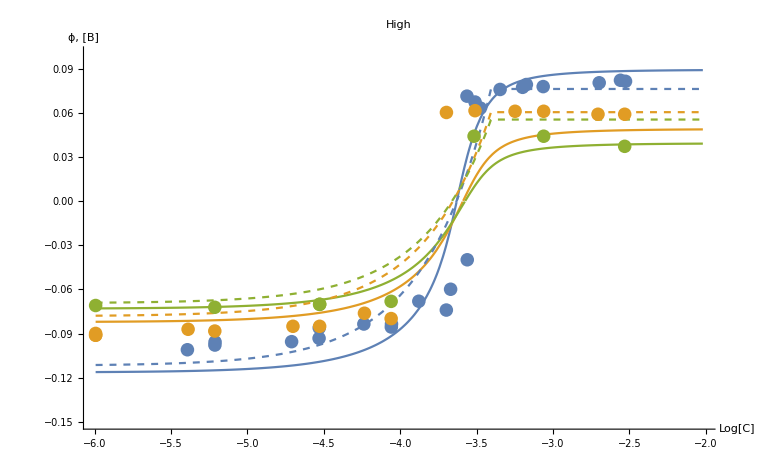

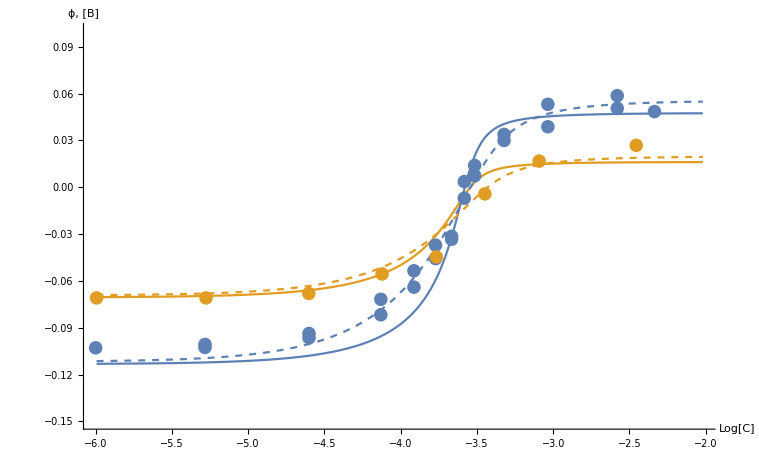

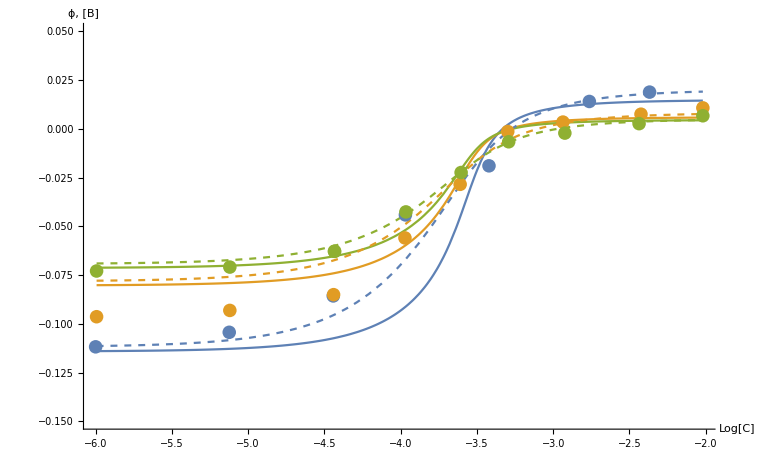

```mathematica
cmin$100=Min[Low$40mM[[All,1]]];cmax$100=Max[Low$40mM[[All,1]]];
pl1=Show[Plot[Evaluate[{F1[10^cc]/.su$Hom$High10mM,F1[10^cc]/.su$Hom$High40mM,F1[10^cc]/.su$Hom$High100mM}/.su$Hom$min],{cc,cmin$100,cmax$100},PlotStyle->colors2,PlotLabel->"High",PlotLegends->Placed[{"Homogeneous 10 mM","Homogeneous 40 mM", "Homogeneous 100 mM"}, {0.2, 0.75}]], Plot[Evaluate[{F[10^cc]/.su$High10mM,F[10^cc]/.su$High40mM,F[10^cc]/.su$High100mM}/.su$min],{cc,cmin$100,cmax$100},PlotStyle->Dashed,PlotLegends->Placed[{"Inhomogeneous 10 mM","Inhomogeneous 40 mM","Inhomogeneous 100 mM"}, {0.2, 0.75}]],ListPlot[{High$10mM,High$40mM, High$100mM },PlotStyle->colors2],PlotRange->{-0.15,0.1},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]

pl2=Show[Plot[Evaluate[{ F1[10^cc]/.su$Hom$Middle10mM,F1[10^cc]/.su$Hom$Middle100mM}/.su$Hom$min],{cc,cmin$100,cmax$100},PlotStyle->colors2], Plot[Evaluate[{ F[10^cc]/.su$Middle10mM,F[10^cc]/.su$Middle100mM}/.su$min],{cc,cmin$100,cmax$100},PlotStyle->Dashed],ListPlot[{ Middle$10mM,Middle$100mM},PlotStyle->colors2],PlotRange->{-0.15,0.1},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]

pl3=Show[Plot[Evaluate[{F1[10^cc]/.su$Hom$Low10mM,F1[10^cc]/.su$Hom$Low40mM,F1[10^cc]/.su$Hom$Low100mM}/.su$Hom$min],{cc,cmin$100,cmax$100},PlotStyle->colors2], Plot[Evaluate[{F[10^cc]/.su$Low10mM,F[10^cc]/.su$Low40mM,F[10^cc]/.su$Low100mM}/.su$min],{cc,cmin$100,cmax$100},PlotStyle->Dashed],ListPlot[{Low$10mM,Low$40mM,Low$100mM},PlotStyle->colors2],PlotRange->{-0.15,0.05},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
```

{0.636107,0.962721,0.96494,3.05943,4.62914,4.63981,9.09035,13.7563,13.788,20.8157,31.5138,33.6125,43.0151,43.2017,48.5848,52.6624,61.7847,61.7847,61.7847,61.7847,61.7847,61.7847,61.7847}

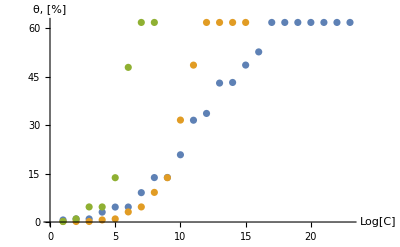

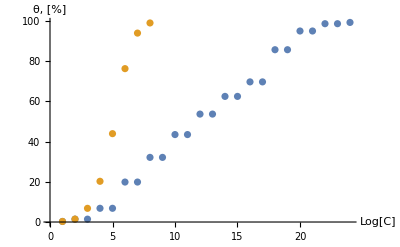

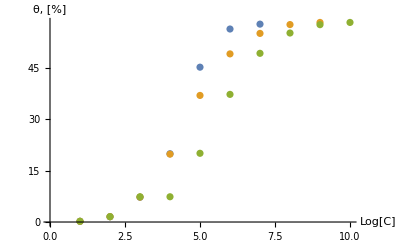

```mathematica
(* Inhomogenous Result{CL->0.47022720996122674,γl->0.8312631776412122,γm->0.9448140526641365,γh->0.4948318804417655,θl->0.5871130558286928,θm->1.,θh->0.6178470405941097,K4$h->24.63279374542971,K4$l->4.288737210950081,K4$m->4.521099348710936};*)
InhomogenousResult={CL->0.47022720996122674,γl->0.8312631776412122,γm->0.9448140526641365,γh->0.4948318804417655,θl->0.5871130558286928,θm->1.,θh->0.6178470405941097,K4$h->24.63279374542971,K4$l->4.288737210950081,K4$m->4.521099348710936};


G[Cc_] =(acl (1 + Cc γ K4 )+2α K4 stot θ$lim - acl √((-8 Cc γ K4^2 stot α θ$lim)/acl + (1 + Cc γ K4 + (2α K4 stot  θ$lim)/acl)^2))/(4α K4 stot)*100;
resultHigh = {K4$h-> 10^24.63279374542971, θ$lim -> 0.6178470405941097,  γ -> 0.4948318804417655, CL->0.47022720996122674};
G[10^High$10mM[[All,1]]]/.su$High10mM/.InhomogenousResult



Show[ListPlot[
{G[10^High$10mM[[All,1]]]/.su$High10mM/.InhomogenousResult,
G[10^High$40mM[[All,1]]]/.su$High40mM/.InhomogenousResult,
G[10^High$100mM[[All,1]]]/.su$High100mM/.InhomogenousResult}, PlotStyle->colors2],AxesLabel->{"Log[C]","θ, [%]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
Show[ListPlot[
{G[10^Middle$10mM[[All,1]]]/.su$Middle10mM/.InhomogenousResult,
G[10^Middle$100mM[[All,1]]]/.su$Middle100mM/.InhomogenousResult}, PlotStyle->colors2],AxesLabel->{"Log[C]","θ, [%]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
Show[ListPlot[
{G[10^Low$10mM[[All,1]]]/.su$Low10mM/.InhomogenousResult,
G[10^Low$40mM[[All,1]]]/.su$Low40mM/.InhomogenousResult,
G[10^Low$100mM[[All,1]]]/.su$Low100mM/.InhomogenousResult}, PlotStyle->colors2],AxesLabel->{"Log[C]","θ, [%]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
```